Goto::nolabel: Label end not found.

Hold[Goto[end]]

{{1}}

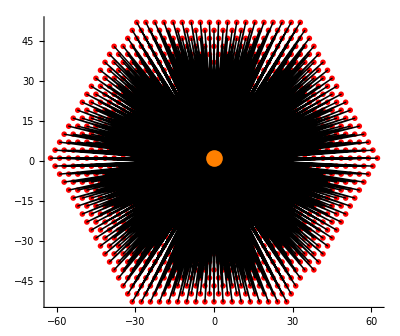

```mathematica
(*----------3 Outer Billiard----------*)
(*----------a) Basic Framework----------*)
xA=0;yA=1; pointA={xA,yA}; textA= Text["A",{0.1,1}];
xB=-(√3)/2;yB=-1/2; pointB={xB,yB}; textB = Text ["B",{-0.92,-0.54}];
xC=(√3)/2; yC=-1/2; pointC={xC,yC}; textC = Text["C",{0.92,-0.54}];
triangle1=Polygon[CirclePoints[3]];
(*---equations[BF]---*)
h[x_]:=1+Sqrt[3]*x;
g[x_]:=1-Sqrt[3]*x;
f:=-0.5;

(*----------START----------*)
(*---------- >>Enter starting parameters<< ----------*)
(*----------b) Starting Point Initialization[START]----------*)
xK=3;yK=1;
n=1000;
pointK={xK,yK}; textK=Text["K",{xK+0.1,yK+0.1}];
(*---Inner Triangle Check[SPI]---*)
If[yK<=h[xK]&&yK<=g[xK]&&yK>=f,
Goto[end];
]

(*----------c) Point Reflection Calculation----------*)
reflectPoint[outPoint_,middlePoint_]:=(
xMove = -(outPoint[[1]]-middlePoint[[1]]);
yMove=-(outPoint[[2]]-middlePoint[[2]]);
{middlePoint[[1]]+xMove,middlePoint[[2]]+yMove}
)
(*---Pointlist Create[PRC]---*)
pointList={pointK};
Do[
xP=First[Last[pointList]];
yP=Last[Last[pointList]];
If[yP<h[xP]&& yP>=g[xP],
AppendTo[pointList,reflectPoint[Last[pointList],pointA]]];
If [yP>=h[xP]&& yP>f,
AppendTo[pointList,reflectPoint[Last[pointList],pointB]]];
If [yP<g[xP]&& yP<=f,
AppendTo[pointList,reflectPoint[Last[pointList],pointC]]];
,n];
(*---Jump to: if triangle check fails[PRC]---*)
Label[end];

(*----------d) Output----------*)
billiardTablePlot={EdgeForm[Directive[Thick,Gray]],LightGray,triangle1,Black,Point[pointA],Point[pointB],Point[pointC],textA,textB,textC,Black,textK,PointSize[0.01],Red,Point[pointList],Black,Line[pointList],PointSize[0.03],Orange,Point[pointK]};
Position[pointList,{xK,yK}]
Show[Graphics[billiardTablePlot],Axes-> True,AxesStyle->Black]
```